```mathematica
KnownPoints={};
```

```mathematica
UpPoint[pnt_]:={Exp[pnt],1+Values[pnt]};
DownPoint[pnt_]:={Log[pnt],Values[pnt]-1};

AddPoint[pnt_,val_]:=(
If[MemberQ[KnownPoints,pnt],
Print["The point " ,pnt," is already known with value " ,Values[pnt] , " and new value is " , val]];

AppendTo[KnownPoints,pnt];
Values[pnt]=val;
);

AddPointChain[pnt_,val_,depth_]:=Module[{cpnt,cval},
AddPoint[pnt,val];
cpnt=pnt;
For[i=0,i<depth,i++,
{cpnt,cval}=UpPoint[cpnt];
AddPoint[cpnt,cval];
];
cpnt=pnt;
For[i=0,i<depth,i++,
{cpnt,cval}=DownPoint[cpnt];
AddPoint[cpnt,cval];
];
];

PlotKnownPoints[rmin_,rmax_]:=Module[{rpoints, rvals, ppoints},
rpoints=Cases[KnownPoints,p_/;Im[p]==0&&rmin≤p≤rmax];
rvals=Values/@rpoints;
ppoints=Transpose[{rpoints,rvals}];
(*Print[Sort[ppoints]];*)
ListPlot[ppoints,DataRange->{rmin,rmax}]
];
```

The point Indeterminate is already known with value -1. and new value is -2.

The point Indeterminate is already known with value -2. and new value is -3.

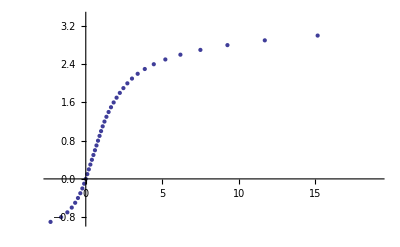

```mathematica
m=0.0;
KnownPoints={};
For[p=m,p<Exp[m],p+=0.1,
AddPointChain[p,p,3]];
PlotKnownPoints[-100,100]
```

```mathematica
m=0;
KnownPoints={};
For[p=m,p<Exp[m],p+=0.1,
r=(p-m)/(Exp[m]-m);
v=(1-r)*m+r*(1+m);
AddPointChain[p,v,3]];
PlotKnownPoints[-100,100]
```

The point ∞ is already known with value -2 and new value is -3

-Graphics-

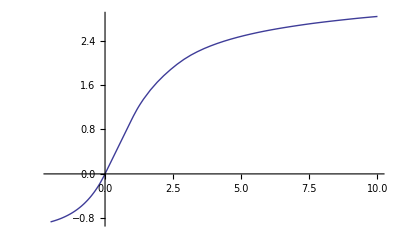

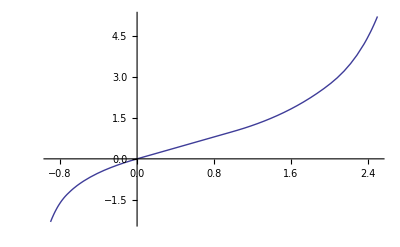

```mathematica
ConstructRealInterpolator:=Module[{rpoints, rvals, ppoints,ipoints},
rpoints=Cases[KnownPoints,p_/;Im[p]==0&&-Infinity<p<Infinity];
rvals=Values/@rpoints;
ppoints=Transpose[{rpoints,rvals}];
ipoints=Transpose[{rvals,rpoints}];
{Interpolation[ppoints],Interpolation[ipoints]}
];

{phi,iphi}=ConstructRealInterpolator;
Plot[phi[x],{x,-2,10}]
Plot[iphi[x],{x,-0.9,2.5}]
```

```mathematica
gexp[x_,p_]:=iphi[p+phi[x]];
SqrtExp[x_]=gexp[x,0.5];
```

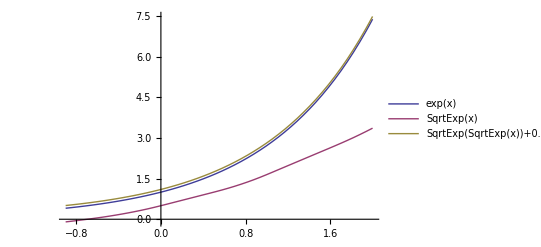

```mathematica
Plot[{Exp[x],SqrtExp[x],SqrtExp[SqrtExp[x]]+0.1},{x,-0.9,2},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{Exp[Exp[x]], Exp[x],gexp[x,p],x,Log[x]},{x,-0.9,10},PlotLegends->"Expressions",PlotRange->{-3,8}],{{p,0.5},-0.3,2}]
```

```mathematica
Manipulate[Plot[{Exp[x],gexp[x,p],x,Log[x]},{x,-2,3},PlotLegends->"Expressions",PlotRange->{-5,5}],{{p,0},-1,1}]
```

InterpolatingFunction::dmval: Input value {-1.25378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.35878} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.50378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.29378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.65378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.20878} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.76878} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.14378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.943781} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.43578} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.64378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.85378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.86378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.42378} lies outside the range of data in the interpolating function. Extrapolation will be used.

## Complex interpolation

```mathematica
ComplexInterpolation[pnts_]:=Module[{rpnts,ipfunc},
rpnts=pnts/.{pnt_?NumberQ,val_}->{{Re[pnt],Im[pnt]},val};
ipfunc=Interpolation[rpnts,InterpolationOrder->1];
ipfunc[Re[#],Im[#]]&
];
```

```mathematica
ComplexInterpolation[{{1+2I,3},{4+5I,6},{7,9}}]
```

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

ipfunc$540820[Re[#1],Im[#1]]&

```mathematica
PlotComplex[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Abs[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Abs",ColorFunction->"TemperatureMap"],
DensityPlot[Arg[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Arg",ColorFunction->"TemperatureMap"]
}]
];
```

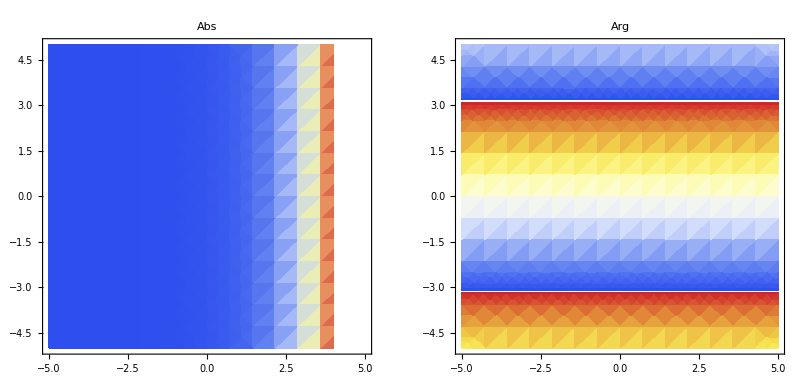

```mathematica
PlotComplex[Exp,{-5-5I,5+5I}]
```

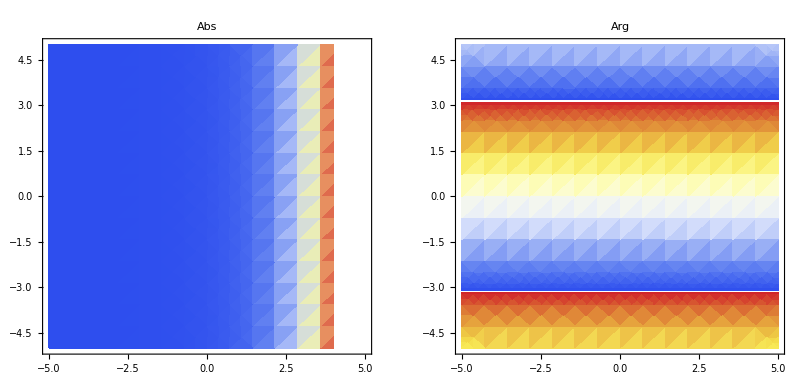

```mathematica
idata=Flatten[Table[{x+y I,Exp[x+y I]},{x,-5,5,0.2},{y,-5,5,0.2}],1];
iexp=ComplexInterpolation[idata];
PlotComplex[iexp,{-5-5I,5+5I}]
```

```mathematica
PlotComplexKnownPoints[rmin_,rmax_]:=Module[{rpoints, cpoints},
rpoints=Cases[KnownPoints,p_/;rmin≤Abs[p]≤rmax];
cpoints=rpoints/.Complex[a_,b_]->{a,b};
ListPlot[cpoints,DataRange->{rmin,rmax}]
];
```

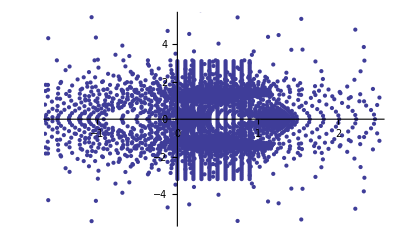

```mathematica
m=0.0;
KnownPoints={};
For[p=m,p<Exp[m],p+=0.1,
For[ip=-3.2,ip<3.2,ip+=0.1,
AddPointChain[p+I*ip,p+I*ip,3]]];
PlotComplexKnownPoints[-10,10]
```

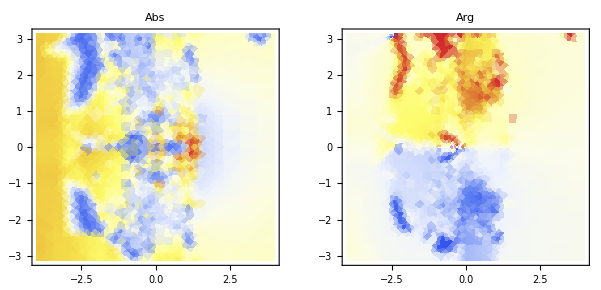

InterpolatingFunction::dmval: Input value {-3.99943, -3.13955} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.42857, -2.69143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

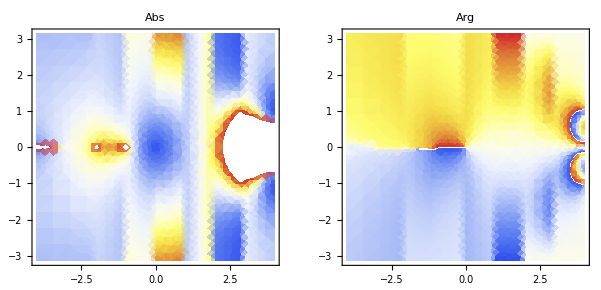

```mathematica
ConstructComplexInterpolator:=Module[{rpoints, rvals, ppoints,ipoints},
rpoints=Cases[KnownPoints,p_/;-Infinity<Abs[p]<Infinity];
rvals=Values/@rpoints;
ppoints=Transpose[{rpoints,rvals}];
ipoints=Transpose[{rvals,rpoints}];
{ComplexInterpolation[ppoints],ComplexInterpolation[ipoints]}
];

{phi,iphi}=ConstructComplexInterpolator;
PlotComplex[phi,{-4-3.14 I,4+3.14 I}]
PlotComplex[iphi,{-4-3.14 I,4+3.14 I}]
```

```mathematica
gexp[x_,p_]:=iphi[p+phi[x]];
SqrtExp[x_]=gexp[x,0.5];
```

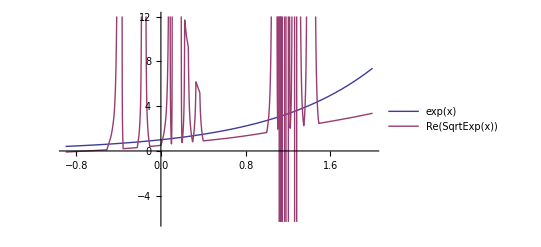

```mathematica
Plot[{Exp[x],Re[SqrtExp[x]]},{x,-0.9,2},PlotLegends->"Expressions"]
```

```mathematica
phi[1.5]
```

1.40521-1.09268×10^-17 ⅈ

```mathematica
IterExp[val_,depth_]:=
Which[
depth==0,val,
depth<0,IterExp[Log[val],depth+1],
depth>0,If[Re[val]<100,IterExp[Exp[val],depth-1],Overflow[]]
];
FindIterDepths[val_]:=Module[{ies,depths,maxdepth=5},
ies=Table[{depth,IterExp[val,depth]},{depth,-maxdepth,maxdepth}];
depths=Cases[ies,{depth_,valu_}:>{-depth,valu}/;0≤ Re[valu]<1];
depths=Sort[depths,Abs[#1[[1]]]<Abs[#2[[1]]]&];
depths
];
FindMinIterDepth[val_]:=FindIterDepths[val][[1,1]];
```

```mathematica
FindIterDepths[-1+2I]//N
```

{{1.,0.804719+2.03444 ⅈ},{-2.,0.81049+0.281705 ⅈ},{2.,0.782903+1.19413 ⅈ},{3.,0.356204+0.990478 ⅈ},{4.,0.0512453+1.22557 ⅈ},{5.,0.204279+1.52901 ⅈ}}

```mathematica
FindMinIterDepth[-15]
```

-1

```mathematica
DensityPlot[FindMinIterDepth[a+b I],{a,-3,3},{b,-5,5},
ColorFunction->"TemperatureMap",PlotLegends->Automatic,
Mesh->All]
```

$Aborted

```mathematica
.
```

$Aborted

```mathematica
.
```

```mathematica
Overflow
```